```mathematica
ClearAll["Global`*"]
```

```mathematica
L:=1
m:=4 (*m=4 очень интересный случай*)
r0:=√((4 L^5)/(3m))
R0:=√((3m L^5)/4)
zL:=0
zR:=0
eps:=10^-10
```

```mathematica
matrLeft:={{6 R0^(1/3), 0, (6R0)/r0,0},{0, -6 R0^(1/3),0,-6 R0^(1/3)},{8/3,0, -2m, 0},{0, -(8R0)/(3r0),0, (8R0)/(3r0)}}
```

```mathematica
{vals, vecs}=Eigensystem[matrLeft]
```

{{4-3 3^(1/6)+√(16+72 3^(1/6)+9 3^(1/3)),-4+3 3^(1/6)-√(64+24 3^(1/6)+9 3^(1/3)),4-3 3^(1/6)-√(16+72 3^(1/6)+9 3^(1/3)),-4+3 3^(1/6)+√(64+24 3^(1/6)+9 3^(1/3))},{{0,1/8 (4+3 3^(1/6)-√(16+72 3^(1/6)+9 3^(1/3))),0,1},{3/8 (4+3 3^(1/6)-√(64+24 3^(1/6)+9 3^(1/3))),0,1,0},{0,1/8 (4+3 3^(1/6)+√(16+72 3^(1/6)+9 3^(1/3))),0,1},{3/8 (4+3 3^(1/6)+√(64+24 3^(1/6)+9 3^(1/3))),0,1,0}}}

```mathematica
posVecs=Pick[vecs, Positive[vals]]
```

{{0,1/8 (4+3 3^(1/6)-√(16+72 3^(1/6)+9 3^(1/3))),0,1},{3/8 (4+3 3^(1/6)+√(64+24 3^(1/6)+9 3^(1/3))),0,1,0}}

```mathematica
bcsLeft={
R[zL]==R0-(Abs[posVecs[[1]][[1]]]+Abs[posVecs[[2]][[1]]])*eps*s,
b[zL]==0-(Abs[posVecs[[1]][[2]]]+Abs[posVecs[[2]][[2]]])*eps,
r[zL]==r0-(Abs[posVecs[[1]][[3]]]+Abs[posVecs[[2]][[3]]])*eps*s,
a[zL]==0+(Abs[posVecs[[1]][[4]]]+Abs[posVecs[[2]][[4]]])*eps
};
```

```mathematica
equations={
R'[z]==6 R[z]^(4/3)(Log[r[z]R[z]]Cos[b[z]]-(a[z]+b[z])Sin[b[z]]),
b'[z]==-6 R[z]^(1/3)(Log[r[z]R[z]]Sin[b[z]]+(a[z]+b[z])Cos[b[z]]),
r'[z]==8/3 R[z]Cos[b[z]]-2m r[z]Cos[a[z]],
a'[z]==2m Sin[a[z]]-(8R[z])/(3r[z])Sin[b[z]]
};
```

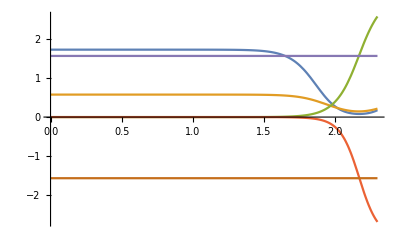

```mathematica
zR:=2.3;
sol=ParametricNDSolveValue[Join[equations, bcsLeft], {R, r, a, b}, {z, zL, zR},{s},Method->"ExplicitRungeKutta",WorkingPrecision->30,MaxSteps->100000,PrecisionGoal->15,AccuracyGoal->15];
ss=9.997;
Plot[{sol[ss][[1]][z],sol[ss][[2]][z],sol[ss][[3]][z],sol[ss][[4]][z], Pi/2, -Pi/2},{z, zL,zR}, PlotRange->Full]
```

```mathematica
f1s[s_?NumericQ]:=Function[x,sol[s][[3]][x]]
f2s[s_?NumericQ]:=Function[x,sol[s][[4]][x]]
x1[s_?NumericQ]:=Module[{res},res=FindMinimum[{(f1s[s][x]-Pi/2)^2,0<=x<zR},{x,3/4*zR} ];
x/. Last[res]]
x2[s_?NumericQ]:=Module[{res},res=FindMinimum[{(f2s[s][x]+Pi/2)^2,0<=x<zR},{x,3/4*zR}];
x/. Last[res]]
res=FindMinimum[{(x1[s]-x2[s])^2,1<=s<=10},{s,4}];
sOpt=s/. Last[res];
res
```

$Aborted

{0.0000131873,{s→9.99719}}

```mathematica
moisei=x1[ss]
```

2.16916

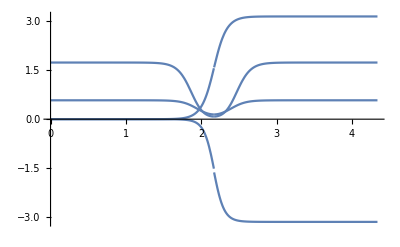

```mathematica
Plot[If[z<=moisei, {sol[ss][[1]][z], sol[ss][[2]][z], sol[ss][[3]][z], sol[ss][[4]][z]}, {sol[ss][[1]][2moisei-z], sol[ss][[2]][2moisei-z], Pi-sol[ss][[3]][2moisei-z],-Pi- sol[ss][[4]][2moisei-z]}], {z, 0, 2moisei}, PlotRange->Full]
```